```mathematica
ResourceFunction["DarkMode"][False]
Needs["Wolfram`Chess`"]
```

```mathematica
size = 3;
players = 2;
board = ConstantArray[0,{size, size}];
getRules[size_]:=Join[Table[i->i+1, {i, size- 1}], Table[i->i - 1, {i, Reverse[Range[size][[2;;]]]}]];
rules = getRules[size];
```

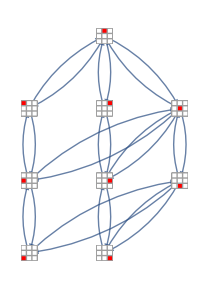

```mathematica
getMove[idx_]:= Select[Replace[idx, #]&/@ rules, #!=idx&];
getMoves[{i_, j_}]:= Join[Map[{#, j}&, getMove[i]], Map[{i, #}&, getMove[j]]];
vertices = Tuples[Range[size], 2];
getEdges[vertice_]:= vertice->#&/@getMoves[vertice]
allEdges = Union[Catenate[getEdges/@ vertices]];
Graph[vertices, allEdges, VertexShapeFunction->(Inset[
ArrayPlot[
ReplacePart[board,#2->1], Mesh->True, ColorRules->{1->Red, 2->Black}
], #1, Center, 8*#3]&), GraphLayout->"LayeredEmbedding"]
```

```mathematica
{{3, 1}, {3, 5}}
```

```mathematica
vertices = Select[Tuples[Range[size], Table[2, players]], #[[1]] != #[[2]]&]
```

{{{1,1},{1,2}},{{1,1},{1,3}},{{1,1},{2,1}},{{1,1},{2,2}},{{1,1},{2,3}},{{1,1},{3,1}},{{1,1},{3,2}},{{1,1},{3,3}},{{1,2},{1,1}},{{1,2},{1,3}},{{1,2},{2,1}},{{1,2},{2,2}},{{1,2},{2,3}},{{1,2},{3,1}},{{1,2},{3,2}},{{1,2},{3,3}},{{1,3},{1,1}},{{1,3},{1,2}},{{1,3},{2,1}},{{1,3},{2,2}},{{1,3},{2,3}},{{1,3},{3,1}},{{1,3},{3,2}},{{1,3},{3,3}},{{2,1},{1,1}},{{2,1},{1,2}},{{2,1},{1,3}},{{2,1},{2,2}},{{2,1},{2,3}},{{2,1},{3,1}},{{2,1},{3,2}},{{2,1},{3,3}},{{2,2},{1,1}},{{2,2},{1,2}},{{2,2},{1,3}},{{2,2},{2,1}},{{2,2},{2,3}},{{2,2},{3,1}},{{2,2},{3,2}},{{2,2},{3,3}},{{2,3},{1,1}},{{2,3},{1,2}},{{2,3},{1,3}},{{2,3},{2,1}},{{2,3},{2,2}},{{2,3},{3,1}},{{2,3},{3,2}},{{2,3},{3,3}},{{3,1},{1,1}},{{3,1},{1,2}},{{3,1},{1,3}},{{3,1},{2,1}},{{3,1},{2,2}},{{3,1},{2,3}},{{3,1},{3,2}},{{3,1},{3,3}},{{3,2},{1,1}},{{3,2},{1,2}},{{3,2},{1,3}},{{3,2},{2,1}},{{3,2},{2,2}},{{3,2},{2,3}},{{3,2},{3,1}},{{3,2},{3,3}},{{3,3},{1,1}},{{3,3},{1,2}},{{3,3},{1,3}},{{3,3},{2,1}},{{3,3},{2,2}},{{3,3},{2,3}},{{3,3},{3,1}},{{3,3},{3,2}}}

```mathematica
MaximalBy[MinimalBy[vertices, #[[1]]&], #[[2]]&]
```

{{{1,1},{3,3}}}

```mathematica
getAwayMoves[{{i1_,j1_} ,{i2_, j2_}}]:= 
Select[Join[
Map[{{i1, j1},{#, j2}}&, getMove[i2]], 
Map[{{i1, j1},{i2, #}}&, getMove[j2]
]],  #[[1]] !=#[[2]]&]
getHomeMoves[{{i1_,j1_} ,{i2_, j2_}}]:= 
Select[Join[
Map[{{#, j1},{i2, j2}}&, getMove[i1]], 
Map[{{i1, #},{i2, j2}}&, getMove[j1]
]], #[[1]] !=#[[2]]&]
```

```mathematica
getAwayEdges[vertice_]:= vertice->#&/@getAwayMoves[vertice]
getHomeEdges[vertice_]:= vertice->#&/@getHomeMoves[vertice]
```

```mathematica
allEdges = Union[Join[Catenate[getHomeEdges/@vertices], Catenate[getAwayEdges/@vertices]]];
```

```mathematica
Length[allEdges]
Length[vertices]
```

336

72

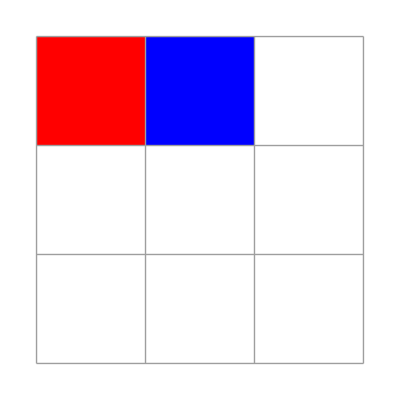
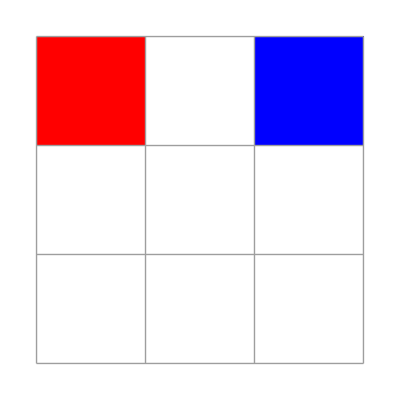
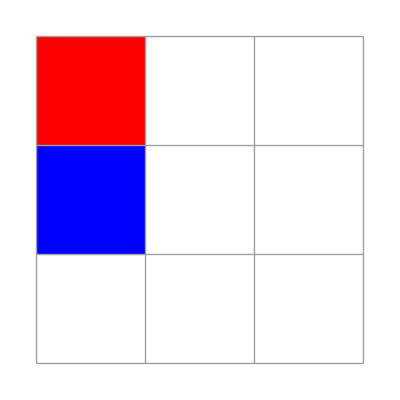
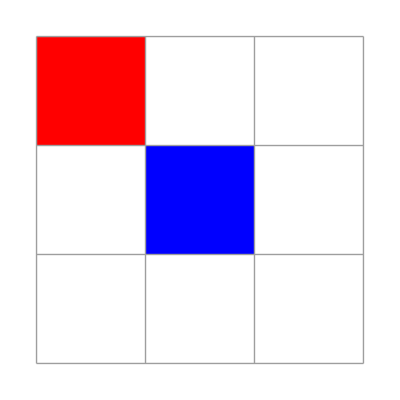
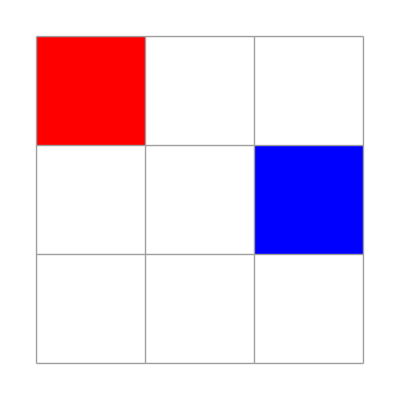
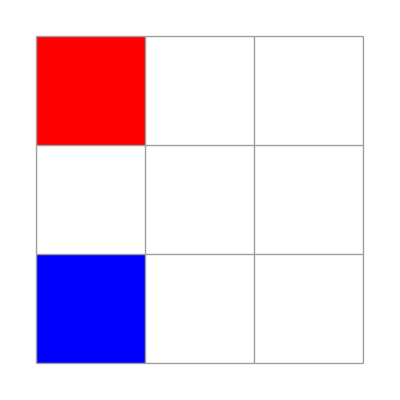
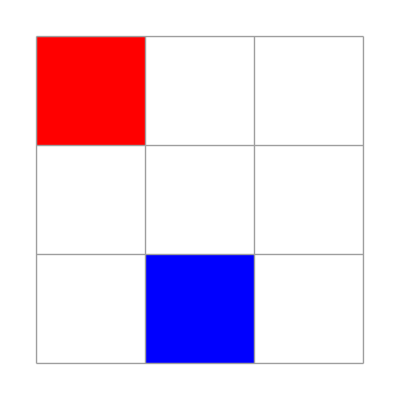
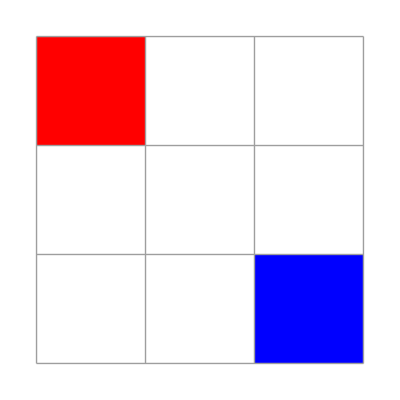
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

ArrayPlot::mat: Argument board at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
g = Graph[vertices, allEdges, VertexShapeFunction->(Inset[
ArrayPlot[
ReplacePart[board,{#2[[1]]->1, #2[[2]]->2}], Mesh->True, ColorRules->{1->Red, 2->Blue}
], #1, Center, 4*#3]&),GraphLayout->"LayeredDigraphEmbedding", EdgeShapeFunction->{{"Arrow","ArrowSize"->.01}}]
```

## Graph of Chess Game

```mathematica
ClearAll["Global`*"]
```

```mathematica
fen = "3Q4/8/8/8/8/8/8/8 w KQkq - 0 1";
board = Chessboard[fen];
board["LegalMoves"]
```

Chessboard[3Q4/8/8/8/8/8/8/8 w KQkq - 0 1][LegalMoves]

#### Functions

```mathematica
getPointsWithinDistance[point_, distance_]:=Select[Flatten[vertices, 1],EuclideanDistance[#,point]<=Sqrt[2]&& #!=point&]
getEdges[source_, dests_]:= source->#&/@ dests
getPathEdges[path_]:=Module[{result = {}},For[i=1, i< Length[path],i+=1, AppendTo[result, path[[i]]->path[[i+1]]]]; result]
```

#### Graph

Establish graph to represent court

```mathematica
vertices = Table[{i, j}, {i, 8}, {j, 8}];
destPoints = getPointsWithinDistance[#, Sqrt[2]]&/@ Flatten[vertices, 1];
edges =MapThread[getEdges[#1, #2]&, {Flatten[vertices, 1], destPoints}];
```

```mathematica
court = Graph[Flatten[vertices, 1],Flatten[edges, 1], VertexCoordinates->Flatten[vertices, 1], GraphHighlight->{{3,5}, {3, 1}}, EdgeStyle->Thin]
```

-Graphics-

Get path from specific vertex

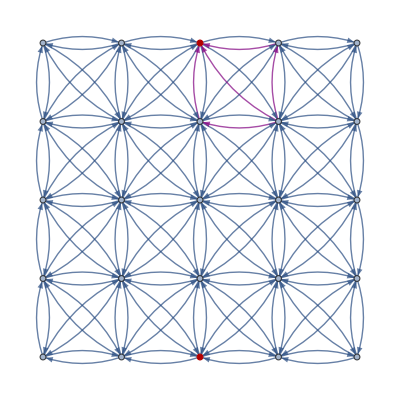

```mathematica
start ={4, 4};
distance = 2;
pathList = FindPath[court,start,{3, 5},distance, 200];
pathEdgesList = getPathEdges/@ pathList;
HighlightGraph[court, Style[#, Purple, Thick]&/@Flatten[pathEdgesList, 1]]
```

## Graph of Basketball Court Attempt Number 2

```mathematica
topKey = {3, 0};
rightWing = {4.5, 0.625};
leftWing = {1.5, 0.625};
leftCorner = {1.25, 2};
rightCorner =  {4.75, 2};
highPost = {3, 0.75};
hoop = {3, 2};
edges = {topKey->leftWing,  topKey->rightWing,  topKey->highPost,topKey->hoop, leftWing->leftCorner, leftWing->highPost,leftWing->topKey, leftWing->hoop, rightWing->topKey, rightWing->highPost,rightWing->rightCorner, rightWing->hoop, highPost->hoop, highPost->leftWing, highPost->leftCorner,highPost->rightWing, highPost->rightCorner, highPost->topKey, leftCorner->hoop, leftCorner->leftWing, leftCorner->highPost, rightCorner->hoop, rightCorner->highPost, rightCorner->rightWing};
allSpots = {topKey, rightWing, leftWing, leftCorner, rightCorner,highPost, hoop};
```

```mathematica
halfCourt = Graph[allSpots, edges, VertexCoordinates->allSpots, GraphHighlight->{hoop}]
```

-Graphics-

```mathematica
maxPasses = 2;
start = highPost;
```

```mathematica
Dynamic[
pathList = FindPath[halfCourt,start,hoop,maxPasses, 10];
pathEdgesList = getPathEdges/@ pathList;
HighlightGraph[halfCourt, Style[#, Purple, Thick]&/@Flatten[pathEdgesList, 1]]
]
```